# Multipolar Expansion

```mathematica
isBuiltIn[s_]:=Context[Evaluate@Head@s]==="System`"
```

```mathematica
myOp[Plus[f_, g_]] := myOp[f] + myOp[g]
myOp[a_?isBuiltIn f_[x_, t_]] := a myOp[f[x, t]]
```

```mathematica
rules={
a___·(b_·c_)·d___/;NumericQ[b]:>b (a·c·d),
a___·(b_ c_)·d___/;NumericQ[b]:>b(a·c·d),
a___·(b_+c_)·d___:>a·b·d+a·c·d,
b_·c_/;Sort[{b,c}]=!={b,c}:>c·b,
CenterDot[a_]:>a
};
```

```mathematica
1·x2·n//.a___·(b_·c_)·d___/;NumericQ[b]:>b (a·c·d)
```

1·x2·n

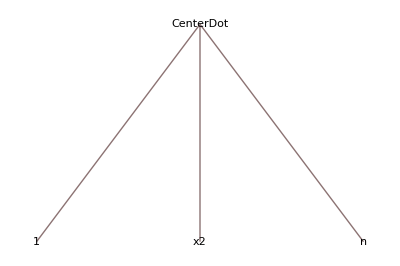

```mathematica
1·x2·n//TreeForm
```

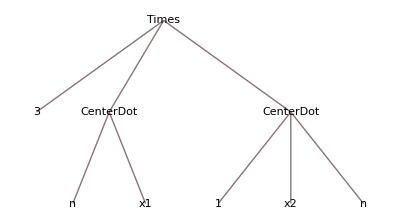

```mathematica
3 n·x1 1·x2·n//TreeForm
```

```mathematica
projection={
x1·x2->Subscript[x, 1] Subscript[x, 2]+Subscript[y, 1] Subscript[y, 2]+Subscript[z, 1] Subscript[z, 2],
x1·x1->(Subscript[x, 1])^2+(Subscript[y, 1])^2+(Subscript[z, 1])^2,
x2·x2->(Subscript[x, 2])^2+(Subscript[y, 2])^2+(Subscript[z, 2])^2,
Subscript[x, 1]->0,
Subscript[x, 2]->0,
Subscript[y, 1]->0,
Subscript[y, 2]->0
};
projectionParallel={
n·x1->Subscript[z, 1],
n·x2->Subscript[z, 2]
};
projectionPerpendicular={
n·x1->0,
n·x2->0
};
projectionTheta={
n·x1->Subscript[x, 1] cθ ,
n·x2->Subscript[x, 2] cθ
};
```

```mathematica
(*
Potential Subscript[V, w] like 1/r^(w+2)
V = Subscript[V, 1]+Subscript[V, 2]+Subscript[V, 3]+...
*)
multipolarPotential[w_]:=1/r^(w+2)∑_(m=If[Mod[w,2]==0,(w+2)/2,(w+1)/2])^(w+1) (-1)^m 2^(m-w-1) (2 m-1)!! ∑_(i=0)^(w+1-m) ∑_(j=0)^(w+1-m-i) ((x1·x1)^i (-2 x1·x2)^j (x2·x2)^(w+1-m-i-j))/(i! j! (w+1-m-i-j)!) ∑_(k=0)^(2 m-w-1) ((x1·n)^(2 m-w-1-k) (-x2·n)^k (1-i,w+1-m j,0 k,0) (1-i,0 j,0 k,2 m-w-1))/(k! (2 m-w-1-k)!)//.rules//FullSimplify
multipolarPotentialProjectedPerpendicular[w_]:=If[Mod[w,2]==0,0,(w!!)/r^(w+2) ∑_(i=0)^((w+1)/2) ∑_(j=0)^((w+1)/2-i) ((-1)^((w+1)/2+j)2^(-(w+1)/2+j)(1-i,(w+1)/2 j,0) (1-i,0 j,0))/(i! j! ((w+1)/2-i-j)!)Subscript[z, 1]^(2i+j)  Subscript[z, 2]^(w+1-2i-j)]//FullSimplify
multipolarPotentialProjectedParallel[w_]:=1/r^(w+2)∑_(m=If[Mod[w,2]==0,(w+2)/2,(w+1)/2])^(w+1) ∑_(i=0)^(w+1-m) ∑_(j=0)^(w+1-m-i) ∑_(k=0)^(2 m-w-1) ((-1)^(j+k+m)2^(m-w-1+j)(2 m-1)!!(1-i,w+1-m j,0 k,0) (1-i,0 j,0 k,2 m-w-1))/(i! j! k!(w+1-m-i-j)!(2 m-w-1-k)!)Subscript[z, 1]^(2i+j+2 m-w-1-k) Subscript[z, 2]^(2(w+1-m-i)-j+k)//FullSimplify
```

```mathematica
Sum[multipolarPotential[a],{a,1,3}]//.rules//Collect[#,r, Simplify]&
```

(-3 n·x1 n·x2+x1·x2)/r^3+(3 (5 (n·x1)^2 n·x2-n·x2 (x1·x1-2 x1·x2)+n·x1 (-5 (n·x2)^2-2 x1·x2+x2·x2)))/(2 r^4)+1/(4 r^5)(-70 (n·x1)^3 n·x2-15 (n·x2)^2 (x1·x1-2 x1·x2)+6 x1·x2 (-(x1·x1)+x1·x2)+15 (n·x1)^2 (7 (n·x2)^2+2 x1·x2-x2·x2)+3 (x1·x1-2 x1·x2) x2·x2+10 n·x1 n·x2 (-7 (n·x2)^2+3 (x1·x1-2 x1·x2+x2·x2)))

```mathematica
expand={
x1·x2->X1 X2+Y1 Y2+Z1 Z2,
x1·x1->(X1)^2+(Y1)^2+(Z1)^2,
x2·x2->(X2)^2+(Y2)^2+(Z2)^2,
a___·n·x1->a·Z1,
a___·n·x2->a·Z2
};
expandTheta={
x1·x2->X1 X2,
x1·x1->(X1)^2,
x2·x2->(X2)^2,
a___·n·x1->cθ a·X1,
a___·n·x2->cθ a·X2
};
```

```mathematica
(-3 n·x1 n·x2+x1·x2)/r^3//.expandTheta//.rules//FullSimplify
```

((1-3 cθ^2) X1 X2)/r^3

```mathematica
(3 (5 (n·x1)^2 n·x2-n·x2 (x1·x1-2 x1·x2)+n·x1 (-5 (n·x2)^2-2 x1·x2+x2·x2)))/(2 r^4)//.expandTheta//.rules//FullSimplify
```

(3 cθ (-3+5 cθ^2) X1 (X1-X2) X2)/(2 r^4)

```mathematica
3 (-2 X1 X2+X2^2+Y2 (-2 Y1+Y2)) Z1-3 (X1^2-2 X1 X2+Y1^2-2 Y1 Y2-2 Z1^2) Z2-6 Z1 Z2^2//Expand
```

-6 X1 X2 Z1+3 X2^2 Z1-6 Y1 Y2 Z1+3 Y2^2 Z1-3 X1^2 Z2+6 X1 X2 Z2-3 Y1^2 Z2+6 Y1 Y2 Z2+6 Z1^2 Z2-6 Z1 Z2^2

```mathematica
1/(4 r^5)(-70 (n·x1)^3 n·x2-15 (n·x2)^2 (x1·x1-2 x1·x2)+6 x1·x2 (-(x1·x1)+x1·x2)+15 (n·x1)^2 (7 (n·x2)^2+2 x1·x2-x2·x2)+3 (x1·x1-2 x1·x2) x2·x2+10 n·x1 n·x2 (-7 (n·x2)^2+3 (x1·x1-2 x1·x2+x2·x2)))//.expandTheta//.rules//FullSimplify
```

-((3-30 cθ^2+35 cθ^4) X1 X2 (2 X1^2-3 X1 X2+2 X2^2))/(4 r^5)

```mathematica
(3 (-2 X1^3 X2+Y1 (X2^2 Y1-2 (X2^2+Y1^2) Y2+3 Y1 Y2^2-2 Y2^3)+X1^2 (3 X2^2+Y2 (-2 Y1+Y2))-4 (X2^2+Y2 (-2 Y1+Y2)) Z1^2-2 X1 X2 (X2^2+(Y1-Y2)^2-4 Z1^2))+8 Z1 (3 ((X1-X2)^2+(Y1-Y2)^2)-2 Z1^2) Z2-12 (X1^2-2 X1 X2+Y1^2-2 Y1 Y2-2 Z1^2) Z2^2-16 Z1 Z2^3)//Expand
```

```mathematica
-6 X1^3 X2+9 X1^2 X2^2-6 X1 X2^3-6 X1 X2 Y1^2+3 X2^2 Y1^2-6 X1^2 Y1 Y2+12 X1 X2 Y1 Y2-6 X2^2 Y1 Y2-6 Y1^3 Y2+3 X1^2 Y2^2-6 X1 X2 Y2^2+9 Y1^2 Y2^2-6 Y1 Y2^3+24 X1 X2 Z1^2-12 X2^2 Z1^2+24 Y1 Y2 Z1^2-12 Y2^2 Z1^2+24 X1^2 Z1 Z2-48 X1 X2 Z1 Z2+24 X2^2 Z1 Z2+24 Y1^2 Z1 Z2-48 Y1 Y2 Z1 Z2+24 Y2^2 Z1 Z2-16 Z1^3 Z2-12 X1^2 Z2^2+24 X1 X2 Z2^2-12 Y1^2 Z2^2+24 Y1 Y2 Z2^2+24 Z1^2 Z2^2-16 Z1 Z2^3//.{Y1->0,Z1->0,Y2->0,Z2->0}
```

-6 X1^3 X2+9 X1^2 X2^2-6 X1 X2^3

```mathematica
(-6 X1^3 X2+9 X1^2 X2^2-6 X1 X2^3)/(4 r^5)//FullSimplify
```

-(3 X1 X2 (2 X1^2-3 X1 X2+2 X2^2))/(4 r^5)